```mathematica
ode=y'[x]-x==0
```

-x+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→x^2/2+C[1]}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

{{y[x]→x^2/2}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

x

```mathematica
dyadx[x_]:=x
```

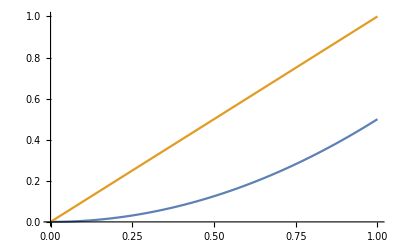

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```